```mathematica
data=Import[NotebookDirectory[]<>"../Data/Table_Equilibrium_tillage0.txt","CSV"];
```

```mathematica
headers=data⟦1⟧;
```

```mathematica
headers
```

{Cost,Het,R,WW,RW,RR}

```mathematica
splidata=SplitBy[data⟦2;;,{1,3,5,6,2}⟧,Last];
```

```mathematica
labels={"A",,"B",,"C"};
```

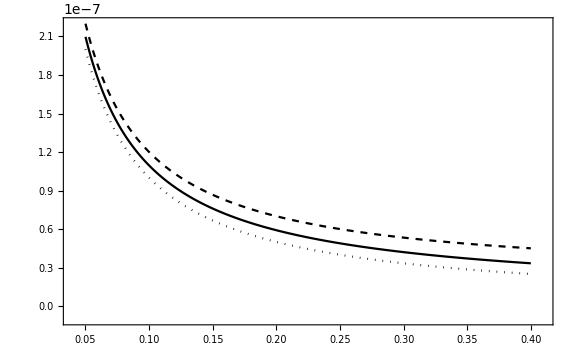

```mathematica
ListPlot[Table[splidata⟦i⟧⟦50;;,{1,2}⟧,{i,{1,3,5}}],PlotRange->{{0.04,0.41},{-10^-8,2.2 10^-7}},Joined->True,Frame->True,PlotStyle->{Directive[Dashed,Black],Directive[Full,Black],Directive[Dotted,Black]},FrameStyle->Directive[Black,Thickness[0.003],Font->"Arial",16],ImageSize->Large]
```

```mathematica
cols={RGBColor["#F2A35E"],RGBColor["#BF766F"]}
```

{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883]}

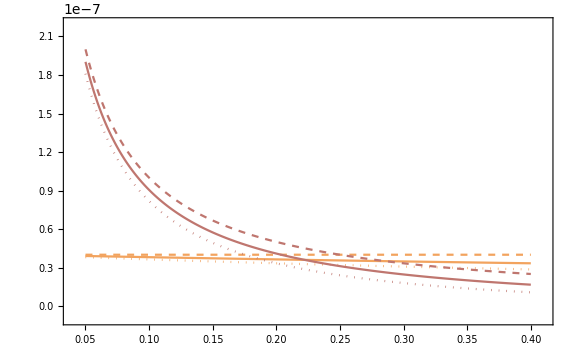

```mathematica
rw=ListPlot[Table[splidata⟦i⟧⟦50;;,{1,3}⟧,{i,{1,3,5}}],PlotRange->{{0.04,0.41},{-10^-8,2.2 10^-7}},Joined->True,Frame->True,PlotStyle->{Directive[Dashed,cols⟦1⟧],Directive[Full,cols⟦1⟧],Directive[Dotted,cols⟦1⟧]},FrameStyle->Directive[Black,Thickness[0.003],Font->"Arial",FontSize->16],ImageSize->Large];
rr=ListPlot[Table[splidata⟦i⟧⟦50;;,{1,4}⟧,{i,{1,3,5}}],PlotRange->{{0.04,0.41},{-10^-8,2.2 10^-7}},Joined->True,Frame->True,PlotStyle->{Directive[Dashed,cols⟦2⟧],Directive[Full,cols⟦2⟧],Directive[Dotted,cols⟦2⟧]},FrameStyle->Directive[Black,Thickness[0.003],Font->"Arial",FontSize->16],ImageSize->Large];
Show[rw,rr,PlotRange->{{0.04,0.41},{-10^-8,2.2 10^-7}},Axes->False]
```

## Insets

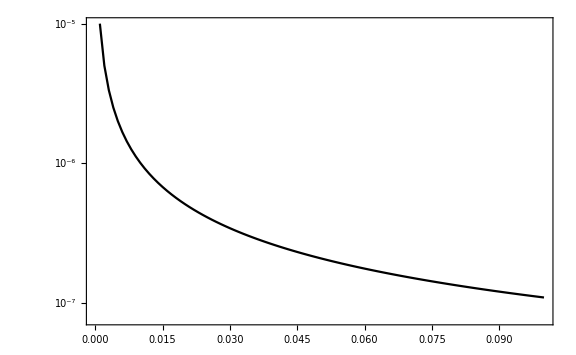

```mathematica
ListLogPlot[splidata⟦3⟧⟦1;;100,{1,2}⟧,PlotRange->All,Joined->True,Frame->True,PlotRange->{Automatic,{1 10^-8,2.2 10^-7}},PlotStyle->Directive[Full,Black],FrameStyle->Directive[Black,Thickness[0.003],Font->"Arial",FontSize->20],FrameLabel->None,ImageSize->Large]
```

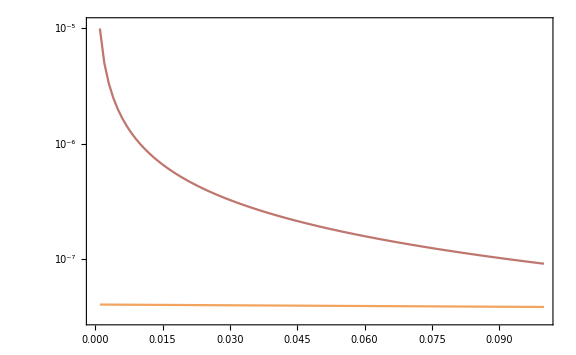

```mathematica
rwlog=ListLogPlot[Table[splidata⟦i⟧⟦1;;100,{1,3}⟧,{i,{3}}],PlotRange->{Automatic,{3 10^-8,1.1 10^-5}},Joined->True,Frame->True,PlotStyle->Directive[Full,cols⟦1⟧],FrameStyle->Directive[Black,Thickness[0.003],Font->"Arial",FontSize->20],FrameLabel->{Style["Fitness cost of resistance c",Black,16],Style["R allele fraction in the long run",Black,16]},ImageSize->Large];
rrlog=ListLogPlot[Table[splidata⟦i⟧⟦1;;100,{1,4}⟧,{i,{3}}],PlotRange->{Automatic,{3 10^-8,1.1 10^-5}},Joined->True,Frame->True,PlotStyle->Directive[Full,cols⟦2⟧],FrameStyle->Directive[Black,Thickness[0.003],Font->"Arial",FontSize->20],FrameLabel->{Style["Fitness cost of resistance c",Black,16],Style["R allele fraction in the long run",Black,16]},ImageSize->Large];
Show[rwlog,rrlog,Axes->False,FrameLabel->None]
```